```mathematica
v1Color=RGBColor["#ff1f5b"];
```

```mathematica
lpColor=RGBColor["#009ade"];
```

```mathematica
lmColor=RGBColor["#f28522"];
```

```mathematica
(*************************)
```

```mathematica
dateMouseSessionListV1toV2m={{"082320","Mouse21060","Session1"},{"090720","Mouse21060","Session2"},{"091120","Mouse21067","Session1"},{"092120","Mouse21067","Session2"},{"101720","Mouse23392","Session2"},{"102520","Mouse23392","Session2"},{"101620","Mouse23393","Session1"},{"101520","Mouse23395","Session1"},{"121320","Mouse23379","Session1"},{"020421","Mouse23320","Session2"},{"020421","Mouse23329","Session2"},{"021321","Mouse23329","Session2"},{"022821","Mouse23329","Session1"},{"030821","Mouse23329","Session1"}};
```

```mathematica
dateMouseSessionListLPtoV2m={{"110120","Mouse23377","Session2"},{"110320","Mouse23377","Session2"},{"110120","Mouse23378","Session1"},{"111820","Mouse23384","Session1"},{"112120","Mouse23384","Session2"},{"103020","Mouse23394","Session1"},{"110220","Mouse23394","Session1"},{"120420","Mouse23378","Session2"},{"120320","Mouse23378","Session1"},{"120520","Mouse23384","Session1"},{"120320","Mouse23384","Session1"},{"121720","Mouse23381","Session1"},{"121920","Mouse23381","Session2"},{"010821","Mouse23339","Session2"},{"011621","Mouse23339","Session1"},{"011621","Mouse23369","Session1"},{"070722","Mouse23067","Session1"},{"070722","Mouse23075","Session1"},{"071022","Mouse23075","Session2"}};
```

```mathematica
dateMouseSessionListLMtoV2m={{"092221","Mouse22422","Session2"},{"100421","Mouse22422","Session2"},{"101121","Mouse22422","Session2"},{"081321","Mouse22437","Session1"},{"081821","Mouse22437","Session2"},{"083021","Mouse22437","Session1"},{"092321","Mouse22472","Session2"},{"101121","Mouse22472","Session1"},{"081921","Mouse22491","Session2"},{"101921","Mouse22436","Session1"},{"102121","Mouse22472","Session2"},{"102821","Mouse22436","Session1"},{"071322","Mouse23025","Session1"},{"071022","Mouse23100","Session1"},{"070822","Mouse23014","Session1"},{"071322","Mouse23014","Session1"},{"070722","Mouse22518","Session1"},{"071522","Mouse22518","Session1"}};
```

```mathematica
(**************************)
```

```mathematica
osiValsV1toV2m=Flatten[ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/Axons/V1toV2m/ValuesForPlotting/osiVals_V1toV2m_nonDupROIs.txt","List"]];
```

```mathematica
osiValsLPtoV2m=Flatten[ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/Axons/LPtoV2m/ValuesForPlotting/osiVals_LPtoV2m_nonDupROIs.txt","List"]];
```

```mathematica
osiValsLMtoV2m=Flatten[ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/Axons/LMtoV2m/ValuesForPlotting/osiVals_LMtoV2m_nonDupROIs.txt","List"]];
```

```mathematica
v1AxonCharts=Show[BoxWhiskerChart[osiValsV1toV2m,{{"Whiskers", Directive[Darker@v1Color,Thick]}, {"Fences", Directive[Darker@v1Color,Thick]},{"MedianMarker", Directive[Darker@v1Color,Thickness[0.009]]}},PlotRange->{All,{0,1}},ChartStyle->Directive[v1Color,Opacity[0.3]],Frame->False],DistributionChart[osiValsV1toV2m,PlotRange->{All,{0,1}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],v1Color],Frame->False],FrameTicks->{{LinTicks[0,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
lmAxonCharts=Show[BoxWhiskerChart[osiValsLMtoV2m,{{"Whiskers", Directive[Darker@lmColor,Thick]}, {"Fences", Directive[Darker@lmColor,Thick]},{"MedianMarker", Directive[Darker@lmColor,Thickness[0.009]]}},PlotRange->{All,{0,1}},ChartStyle->Directive[lmColor,Opacity[0.3]],Frame->False],DistributionChart[osiValsLMtoV2m,PlotRange->{All,{0,1}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],lmColor],Frame->False],FrameTicks->{{LinTicks[0,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
lpAxonCharts=Show[BoxWhiskerChart[osiValsLPtoV2m,{{"Whiskers", Directive[Darker@lpColor,Thick]}, {"Fences", Directive[Darker@lpColor,Thick]},{"MedianMarker", Directive[Darker@lpColor,Thickness[0.009]]}},PlotRange->{All,{0,1}},ChartStyle->Directive[lpColor,Opacity[0.3]],Frame->False],DistributionChart[osiValsLPtoV2m,PlotRange->{All,{0,1}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],lpColor],Frame->False],FrameTicks->{{LinTicks[0,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
transp=Show[BoxWhiskerChart[osiValsLPtoV2m,{{"Whiskers", Directive[Transparent,Thick]}, {"Fences", Directive[Transparent,Thick]},{"MedianMarker", Directive[Transparent,Thickness[0.009]]}},PlotRange->{All,{0,1}},ChartStyle->Transparent,Frame->False],DistributionChart[osiValsLPtoV2m,PlotRange->{All,{0,1}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],Transparent],Frame->False],FrameTicks->{{LinTicks[0,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Black,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

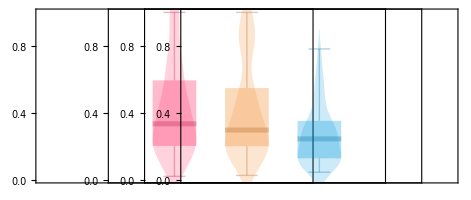

```mathematica
GraphicsRow[{v1AxonCharts,lmAxonCharts,lpAxonCharts,transp},Spacings->{{-280,-280,-280,-400}}]
```

```mathematica
(**********************)
```

```mathematica
dsiValsV1toV2m=Flatten[ToExpression/@Import["C:/Users/garrett/Desktop/PopulationAnalyses/Observational/Axons/V1toV2m/ValuesForPlotting/dsiVals_V1toV2m_nonDupROIs.txt","List"]];
```

```mathematica
dsiValsLPtoV2m=Flatten[ToExpression/@Import["C:/Users/garrett/Desktop/PopulationAnalyses/Observational/Axons/LPtoV2m/ValuesForPlotting/dsiVals_LPtoV2m_nonDupROIs.txt","List"]];
```

```mathematica
dsiValsLMtoV2m=Flatten[ToExpression/@Import["C:/Users/garrett/Desktop/PopulationAnalyses/Observational/Axons/LMtoV2m/ValuesForPlotting/dsiVals_LMtoV2m_nonDupROIs.txt","List"]];
```

```mathematica
v1AxonCharts=Show[BoxWhiskerChart[dsiValsV1toV2m,{{"Whiskers", Directive[Darker@v1Color,Thick]}, {"Fences", Directive[Darker@v1Color,Thick]},{"MedianMarker", Directive[Darker@v1Color,Thickness[0.009]]}},PlotRange->{All,{0,1}},ChartStyle->Directive[v1Color,Opacity[0.3]],Frame->False],DistributionChart[dsiValsV1toV2m,PlotRange->{All,{0,1}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],v1Color],Frame->False],FrameTicks->{{LinTicks[0,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
lmAxonCharts=Show[BoxWhiskerChart[dsiValsLMtoV2m,{{"Whiskers", Directive[Darker@lmColor,Thick]}, {"Fences", Directive[Darker@lmColor,Thick]},{"MedianMarker", Directive[Darker@lmColor,Thickness[0.009]]}},PlotRange->{All,{0,1}},ChartStyle->Directive[lmColor,Opacity[0.3]],Frame->False],DistributionChart[dsiValsLMtoV2m,PlotRange->{All,{0,1}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],lmColor],Frame->False],FrameTicks->{{LinTicks[0,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
lpAxonCharts=Show[BoxWhiskerChart[dsiValsLPtoV2m,{{"Whiskers", Directive[Darker@lpColor,Thick]}, {"Fences", Directive[Darker@lpColor,Thick]},{"MedianMarker", Directive[Darker@lpColor,Thickness[0.009]]}},PlotRange->{All,{0,1}},ChartStyle->Directive[lpColor,Opacity[0.3]],Frame->False],DistributionChart[dsiValsLPtoV2m,PlotRange->{All,{0,1}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],lpColor],Frame->False],FrameTicks->{{LinTicks[0,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
transp=Show[BoxWhiskerChart[dsiValsLPtoV2m,{{"Whiskers", Directive[Transparent,Thick]}, {"Fences", Directive[Transparent,Thick]},{"MedianMarker", Directive[Transparent,Thickness[0.009]]}},PlotRange->{All,{0,1}},ChartStyle->Transparent,Frame->False],DistributionChart[dsiValsLPtoV2m,PlotRange->{All,{0,1}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],Transparent],Frame->False],FrameTicks->{{LinTicks[0,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Black,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

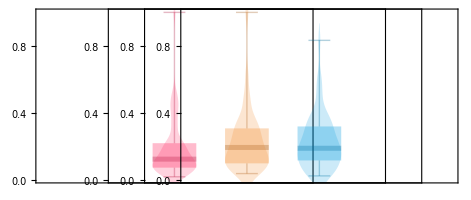

```mathematica
GraphicsRow[{v1AxonCharts,lmAxonCharts,lpAxonCharts,transp},Spacings->{{-280,-280,-280,-400}}]
```